```mathematica
Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/SEIQREpidemiologyModel.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelModifications.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelingVisualizationFunctions.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/WL/SystemDynamicsInteractiveInterfacesFunctions.m"];
```

```mathematica
Clear[modelSEIQR];
modelSEIQR = 
  SEIQRModel[t, "InitialConditions" -> True, "RateRules" -> True, 
   "TotalPopulationRepresentation" -> "Constant"];
ModelGridTableForm[modelSEIQR]
```

<|Stocks→# | Symbol | Description
1 | NP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | IP[t] | Infected Population
5 | QP[t] | Quarantined Population
6 | RP[t] | Recovered Population,Rates→# | Symbol | Description
1 | β | Contact rate for the infected population
2 | α1 | Proportion of Exposed to Infected Rate (Confirmed)
3 | α2 | Proportion Sent to Quarantine (Suspected)
4 | φ | Proportion of not detected after medical diagnosis (Discarded)
5 | τ | Proportion from Suspected to Recovered class
6 | γ | Recovery Rate
7 | ζ | Average Incubation Period
8 | λ | Average Infection Period,Equations→# | Equation
1 | SP'[t]==φ QP[t]-(β IP[t] SP[t])/NP[0]
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/NP[0]
3 | IP'[t]==α1 EP[t]-γ IP[t]
4 | QP'[t]==α2 EP[t]-(τ+φ) QP[t]
5 | RP'[t]==γ IP[t]+τ QP[t],RateRules→# | Symbol | Value
1 | NP[0] | 100000
2 | β | 6.×10^-6
3 | α1 | 1/ζ
4 | α2 | 1/ζ
5 | φ | 0.2
6 | τ | γ
7 | γ | 1/λ
8 | ζ | 13
9 | λ | 31/4,InitialConditions→# | Equation
1 | SP[0]==99999
2 | EP[0]==0
3 | IP[0]==1
4 | QP[0]==0
5 | RP[0]==0|>

## Getting Data

```mathematica
cievsPEData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/Pernambuco/Monkeypox%20-%20Pernambuco.csv", 
   "Dataset", "HeaderLines" -> 1];
cievsRECData :=Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/Recife/Monkeypox%20-%20Recife.csv", "Dataset", 
   "HeaderLines" -> 1];
owdPEData := Import["https://raw.githubusercontent.com/globaldothealth/monkeypox/main/latest_deprecated.csv", "Dataset", "HeaderLines" -> 1];

dateFormat = {"Day", "/", "Month", "/", "Year"};
PEdataMap = cievsPEData // Normal;
RECdataMap = cievsRECData // Normal;
owdPEDataMap = Query[Select[StringContainsQ[ #Country, "Brazil"] && StringContainsQ[#Location, "Pernambuco"] && StringContainsQ[#Status, "confirmed"]&]] @ owdPEData;
```

#### Populações

```mathematica
(*pernambucoEntity = Entity["AdministrativeDivision", {"Pernambuco", "Brazil"}];
recifeEntity = Entity["City", {"Recife", "Pernambuco", "Brazil"}];
popProperty = "Population";*)

pernambucoPopulation = QuantityMagnitude[9674793]; (*IBGE 2022 - https://www.ibge.gov.br/cidades-e-estados/pe.html*)
recifePopulation =  QuantityMagnitude[1661017]; (*IBGE 2022 - https://www.ibge.gov.br/cidades-e-estados/pe.html*)
maleInfected = 80.6/100;(*Cievs/PE. Dados atualizados em 03.11.2022, 15h.*)

(*Clear[Smooth];*)
(*Smooth[data_] := MovingMap[Ceiling[Mean[#]]&, data, {{7, "Day"}, Left, "Week"}, Automatic];*)
```

```mathematica
estimatedInitialSusceptiblePopulation = ((recifePopulation/pernambucoPopulation)*maleInfected)*recifePopulation
```

229848.

#### Confirmados

{Thu 21 Jul 2022→2,Fri 29 Jul 2022→4,Fri 5 Aug 2022→3,Sat 6 Aug 2022→3,Fri 12 Aug 2022→2,Tue 16 Aug 2022→1,Thu 18 Aug 2022→3,Wed 24 Aug 2022→4,Fri 26 Aug 2022→1,Mon 29 Aug 2022→1,Wed 31 Aug 2022→3,Thu 1 Sep 2022→14,Sun 4 Sep 2022→6,Tue 6 Sep 2022→1,Thu 8 Sep 2022→8,Fri 9 Sep 2022→4,Tue 13 Sep 2022→7,Wed 14 Sep 2022→23,Thu 15 Sep 2022→5,Fri 16 Sep 2022→12,Sat 17 Sep 2022→4,Tue 20 Sep 2022→7,Fri 23 Sep 2022→8,Tue 27 Sep 2022→2,Fri 30 Sep 2022→16,Tue 4 Oct 2022→10,Fri 7 Oct 2022→10,Tue 11 Oct 2022→0,Fri 14 Oct 2022→0,Tue 18 Oct 2022→1,Fri 21 Oct 2022→0,Tue 25 Oct 2022→3,Fri 28 Oct 2022→10,Tue 1 Nov 2022→8,Fri 4 Nov 2022→24}

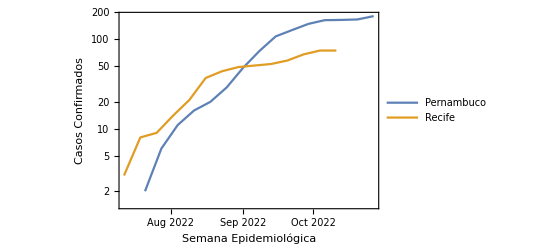

```mathematica
groupedByDateOWD = GroupBy[Normal[owdPEDataMap], FromDateString[#"Date_confirmation", {"Year", "-", "Month", "-", "Day"}]&,Length] // Normal;
groupedCievs= Map[FromDateString[#Inicio, dateFormat]-> #"Confirmados" &,PEdataMap];
confirmadosJoined = Union[groupedByDateOWD, Take[groupedCievs, {15,-1}]] 
totalJoinedSmoothed = Smooth[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]]];
(*totalConfirmadosOWDPE=Smooth[Accumulate[TimeSeries[groupedByDateOWD, TemporalRegularity->True]]];*)
totalConfirmadosPE = 
    Smooth[Accumulate[
TimeSeries[
Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"} &,PEdataMap], 
TemporalRegularity -> True]]];
totalConfirmadosREC = 
 Smooth[Accumulate[
TimeSeries[
     Map[{FromDateString[#Inicio, dateFormat], #Confirmados} &, 
      RECdataMap],TemporalRegularity -> True]]];
DateListLogPlot[Tooltip[{totalJoinedSmoothed ,totalConfirmadosREC} ], 
 Joined -> True, PlotLegends -> {"Pernambuco", "Recife"}, 
 PlotMarkers -> False, GridLines -> Keys[confirmadosJoined],FrameLabel->{"Semana Epidemiológica","Casos Confirmados"}]
```

#### Prováveis

```mathematica
totalProvaveisPE = 
 Smooth[Accumulate[
TimeSeries[
     Map[{FromDateString[#Inicio, dateFormat], #"Prováveis"} &, 
      PEdataMap], TemporalRegularity -> True]]];
totalProvaveisREC = 
Smooth[Accumulate[
TimeSeries[
     Map[{FromDateString[#Inicio, dateFormat], #"Prováveis"} &, RECdataMap], TemporalRegularity -> True]]];
DateListLogPlot[Tooltip[{totalProvaveisPE, totalProvaveisREC} ], 
 Joined -> True, PlotLegends -> {"Pernambuco", "Recife"}, 
 PlotMarkers -> Automatic, GridLines -> Automatic];
```

#### Suspeitos

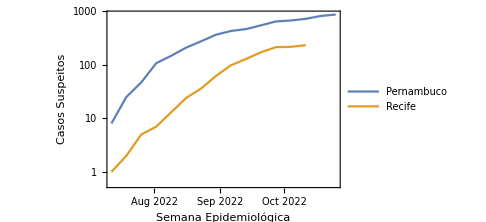

```mathematica
totalSuspeitosPE = 
  Smooth[Accumulate[
TimeSeries[
     Map[{FromDateString[#Inicio, dateFormat], #"Suspeitos"} &, 
      PEdataMap],TemporalRegularity -> True]]];
totalSuspeitosREC = 
Smooth[Accumulate[
TimeSeries[
     Map[{FromDateString[#Inicio, dateFormat], #"Suspeitos"} &, RECdataMap], TemporalRegularity -> True]]];
DateListLogPlot[Tooltip[{totalSuspeitosPE, totalSuspeitosREC} ], 
 Joined -> True, PlotLegends -> {"Pernambuco", "Recife"}, 
 PlotMarkers -> False, FrameLabel->{"Semana Epidemiológica","Casos Suspeitos"},ImageSize->Medium,GridLines -> False]
```

#### Notificados

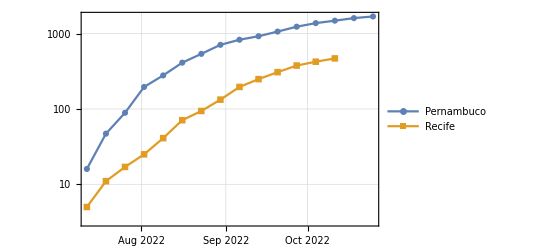

Keys::invrl: The argument joined is not a valid Association or a list of rules.

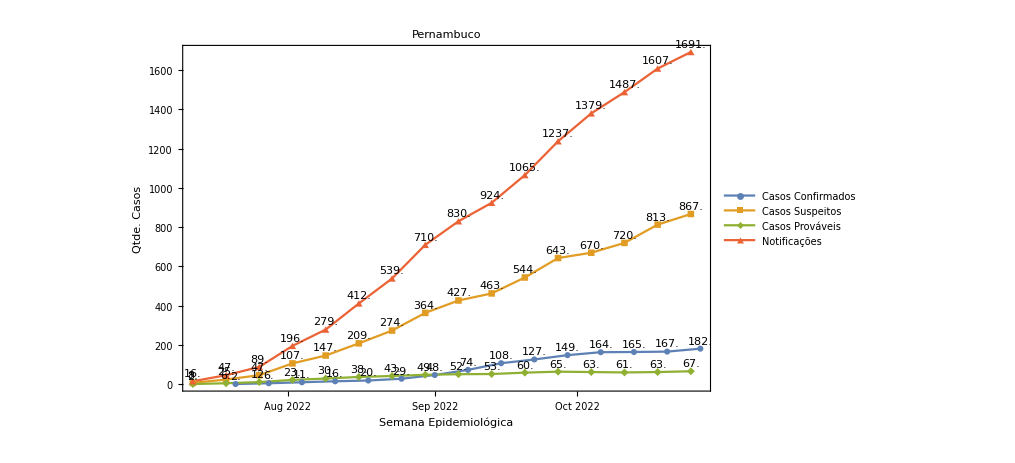

```mathematica
totalNotificadosPE = 
Smooth[Accumulate[
TimeSeries[
     Map[{FromDateString[#Inicio, dateFormat], #"Notificados"} &, 
      PEdataMap],TemporalRegularity -> True]]];
totalNotificadosREC = 
Smooth[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Notificados"} &, RECdataMap],TemporalRegularity -> True]]];
DateListLogPlot[Tooltip[{totalNotificadosPE, totalNotificadosREC} ],  Joined -> True, PlotLegends -> {"Pernambuco", "Recife"},  PlotMarkers -> Automatic, GridLines -> Automatic]

DateListPlot[{totalJoinedSmoothed ,totalSuspeitosPE, totalProvaveisPE, totalNotificadosPE}->{#2&},LabelingFunction->(Placed[Last@#1,Above]&), 
 Joined -> True, PlotLegends -> {"Casos Confirmados", "Casos Suspeitos", "Casos Prováveis", "Notificações" }, 
 PlotMarkers -> Automatic, GridLines -> Keys[joined],FrameLabel->{"Semana Epidemiológica","Qtde. Casos"}, PlotLabel->"Pernambuco"]
```

## Dados Literatura

Alguns dados que tirei de  artigos sobre a dinâmica da Monkeypox que serão uteis para as formulas

#### Periodo de Incubação

```mathematica
incubation = Range[5, 21];
incubationPeriod = Mean[incubation];
incubationPeriod
```

13

#### Período de Infecção [1]

```mathematica
prodomalPhase = Range[0, 3];
rashPhase = Range[7, 21];
infectiousPeriod = Mean[Map[Median] @ {prodomalPhase, rashPhase}]
maxInfectiousPeriod = Max[prodomalPhase, rashPhase]
medianInfectiousPeriod = Flatten[ {prodomalPhase,rashPhase}]
```

31/4

21

{0,1,2,3,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

#### Taxa de Recuperação (γ)

De acordo com [2], γ ==1/λ, sendo λ a média do período de infecção total.

## Modelos

```mathematica
initialInfected =  Normal[totalJoinedSmoothed][[1]][[2]]
initialExposed = Normal[totalProvaveisPE][[1]][[2]]
initialQuarantine = Normal[totalSuspeitosPE][[1]][[2]]
realEPData =  <|"Exposed"-> Ceiling[totalSuspeitosPE["Values"]] // Normal|>
realIPData = <|"Infected"-> Ceiling[totalJoinedSmoothed["Values"]] // Normal|>
realQPData = <|"Quarantine"-> Ceiling[totalProvaveisPE["Values"]] // Normal|>
allData = Join[realEPData,realIPData,realQPData]
lsFocusParams = {β, ζ, λ};
```

2

2

8

<|Exposed→{8,25,47,107,147,209,274,364,427,463,544,643,670,720,813,867}|>

<|Infected→{2,6,11,16,20,29,48,74,108,127,149,164,165,167,182}|>

<|Quarantine→{2,6,12,23,30,38,43,49,52,53,60,65,63,61,63,67}|>

<|Exposed→{8,25,47,107,147,209,274,364,427,463,544,643,670,720,813,867},Infected→{2,6,11,16,20,29,48,74,108,127,149,164,165,167,182},Quarantine→{2,6,12,23,30,38,43,49,52,53,60,65,63,61,63,67}|>

```mathematica
modelSEIQR = SetRateRules[modelSEIQR, <|NP[0] -> estimatedInitialSusceptiblePopulation|>];
modelSEIQR = SetInitialConditions[modelSEIQR,
   <|SP[0] -> estimatedInitialSusceptiblePopulation -initialExposed- initialInfected-initialQuarantine,
    EP[0] -> initialExposed,
    IP[0] -> initialInfected,
    QP[0] -> initialQuarantine
    |>]; (* Subtrair do número da primeira semana epidemiológica*)
lsActualEquations = 
  Join[modelSEIQR["Equations"] //. 
    KeyDrop[modelSEIQR["RateRules"], lsFocusParams], 
   modelSEIQR["InitialConditions"]];
ResourceFunction["GridTableForm"][List /@ lsActualEquations]
```

# | 1
1 | SP'[t]==0.2 QP[t]-4.35069×10^-6 β IP[t] SP[t]
2 | EP'[t]==-(2 EP[t])/ζ+4.35069×10^-6 β IP[t] SP[t]
3 | IP'[t]==EP[t]/ζ-IP[t]/λ
4 | QP'[t]==EP[t]/ζ-(0.2+1/λ) QP[t]
5 | RP'[t]==IP[t]/λ+QP[t]/λ
6 | SP[0]==229836.
7 | EP[0]==2
8 | IP[0]==2
9 | QP[0]==8
10 | RP[0]==0

```mathematica
aSol = Association@
  Flatten@ParametricNDSolve[lsActualEquations, 
    Head /@ Keys[modelSEIQR["Stocks"]], {t, 0,52}, lsFocusParams];
```

```mathematica
opts = {PlotRange -> All, PlotLegends -> None, PlotTheme -> "Detailed", 
   PerformanceGoal -> "Speed", ImageSize -> 400};
lsPopulationKeys = GetPopulationSymbols[modelSEIQR, __ ~~ "Population"];
Manipulate[
 DynamicModule[{lsPopulationPlots}, 
  lsPopulationPlots = 
   ParametricSolutionsPlots[modelSEIQR["Stocks"], 
    KeyTake[aSol, lsPopulationKeys], {contactRate, incubationPeriod, 
     infectionPeriod}, nWeeks,
    "LogPlot" -> popLogPlotQ, "Together" -> popTogetherQ, 
    "Derivatives" -> popDerivativesQ, "DerivativePrefix" -> "Δ",
     opts];
 
  Multicolumn[lsPopulationPlots, nPlotColumns, Dividers -> All, 
   FrameStyle -> GrayLevel[0.8]]],
   
 {{contactRate, 6.3, StringJoin["Contact rate of the infected population (β) ", ToString[DisplayForm[InterpretationBox[SuperscriptBox["10", "-4"], var]]]]}, 1, 10, 1, 
  Appearance -> {"Open"}},
 {{incubationPeriod, 13, "Incubation period (ζ) in days"}, 5, 21, 1, 
  Appearance -> {"Open"}},
 {{infectionPeriod, 8, "Infection Period (λ) in days"}, 0, 21, 1, 
  Appearance -> {"Open"}},
 {{nWeeks,28, "Epidemiological Week"}, 1, 52, 1, Appearance -> {"Open"}},
 {{popTogetherQ, True, "Plot populations together"}, {False, True}},
 {{popDerivativesQ, False, "Plot populations derivatives"}, {False, True}},
 {{popLogPlotQ, False, "LogPlot populations"}, {False, True}},
 {{nPlotColumns, 2, "Number of plot columns"}, Range[3]}, 
 ControlPlacement -> Left, ContinuousAction -> False]
```

```mathematica
(*Clear[PadRealData];
PadRealData[aData:Association[ (_String -> _?VectorQ)..],incubationPeriod_?IntegerQ,infectiousPeriod_?IntegerQ]:=
Block[{},
Join[ConstantArray[0,incubationPeriod+infectiousPeriod],#]&/@aData];*)
```

```mathematica
opts={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->800};
Manipulate[
DynamicModule[{modelSEIQR=modelSEIQR,equations,aSol,lsPopulationPlots},
modelSEIQR = SetRateRules[modelSEIQR, <|NP[0] -> population|>];
modelSEIQR = SetInitialConditions[modelSEIQR,
   <|SP[0] ->  population -initialExposed- initialInfected-initialQuarantine,
    EP[0] -> initialExposed,
    IP[0] -> initialInfected,
    QP[0] -> initialQuarantine
    |>];
equations=Join[modelSEIQR["Equations"]//.KeyDrop[modelSEIQR["RateRules"],lsFocusParams],modelSEIQR["InitialConditions"]];
aSol=Association@Flatten@
ParametricNDSolve[equations,{SP,EP,IP,QP, RP},{t,0,100},lsFocusParams];

lsPopulationPlots=
ParametricSolutionsPlots[
modelSEIQR["Stocks"],
KeyTake[aSol,GetPopulationSymbols[modelSEIQR, __ ~~ "Population"]],
{contactRate, incubationPeriod,infectionPeriod},nWeeks,"Together"->False,opts];
    
Show[lsPopulationPlots⟦3⟧,ListPlot[PadRealData[realIPData,Round[incubationPeriod+padOffset],Round[infectionPeriod+padOffset]],PlotStyle->{Blue,Black,Red}]]
],
{{population,estimatedInitialSusceptiblePopulation/100,"Population"},100,estimatedInitialSusceptiblePopulation,50,Appearance->{"Open"}},
{{padOffset,0,"real data padding offset"},-100,100,1,Appearance->{"Open"}},
 {{contactRate, 0.01, StringJoin["Contact rate of the infected population (β)", ToString[DisplayForm[InterpretationBox[SuperscriptBox["10", "-4"], var]]]]}, 0.01, 2, 0.01, 
  Appearance -> {"Open"}},
 {{incubationPeriod, 13, "Incubation period (ζ) in days "}, 5, 21, 1, 
  Appearance -> {"Open"}},
 {{infectionPeriod, 7, "Infection Period (λ) in days"}, 0, 21, 1, 
  Appearance -> {"Open"}},
 {{nWeeks,28, "Epidemiological Week (t)"}, 1, 52, 1, Appearance -> {"Open"}},
 {{nPlotColumns, 2, "Number of plot columns"}, Range[3]}, 
ControlPlacement->Left,ContinuousAction->False]
```

### Otimização de β

```mathematica
(* time is measured in Days *)
(*toModelTime[t0_DateObject, date_DateObject] := 
	QuantityMagnitude[DateDifference[t0, date]]
toDataDate[t0_DateObject, time:(_Integer|_Real)] := 
	DatePlus[t0, time]*)
```

```mathematica
(*ClearAll[fitWithDataPlot]
fitWithDataPlot[fit_FittedModel, {dateMin_DateObject, dateMax_DateObject}] := 
 Module[{plotData, bands, cd = ColorData[108]},
  plotData = {toDataDate[dateMin, #1], #2} & @@@ fit["Data"];
  bands[x_] = 
   Quiet[fit["SinglePredictionBands", ConfidenceLevel -> 0.95] /. t -> x];
  Show[
    DateListPlot[plotData,
     Joined -> False,
     PlotRange -> All
     ],
    Plot[{fit[toModelTime[dateMin, FromAbsoluteTime@t]], 
      bands[toModelTime[dateMin, FromAbsoluteTime@t]]}, {t, 
      AbsoluteTime@dateMin, AbsoluteTime@dateMax},
     PlotRange -> All,
     PlotStyle -> {cd[2], None},
     Filling -> {2 -> {1}},
     FillingStyle -> {Opacity[0.5, Lighter@cd[2]]}
     ],
    PlotRange -> All,
    PlotRangePadding -> {Automatic, {Scaled[0.03], Scaled[0.1]}},
    FrameLabel -> {"time (d)", "number infected"},
    PlotLabel -> 
     StringForm["Estimated variance = ``", fit["EstimatedVariance"]],
    ImageSize -> 360
    ] // Labeled[#, 
     Column[{PointLegend[{cd[1]}, {"observed"}], 
       LineLegend[{cd[2]}, {"calculated"}], 
       SwatchLegend[{Opacity[0.5, Lighter@cd[2]]}, {"95% prediction band"}]}, 
      Left], Right] &
  ]*)
```

```mathematica
(*ClearAll[modelSensitivityPlot]
modelSensitivityPlot[modelIn:(_ParametricFunction[__]),fit_FittedModel,{{tMin_?NumberQ,tMax_?NumberQ},{yMin_?NumberQ,yMax_?NumberQ}},scale:{__?NumberQ}]:=Module[{model,sensitivities,cd=ColorData[108],params,t},params=fit["BestFitParameters"];
model=modelIn[t]/. params;
sensitivities=MapThread[model+(#2 {-1,1} D[modelIn,#1][t]/. params)&,{Keys@params,scale}];
TabView@MapThread[Function[{p,bands,sf},p->(Show[ListPlot[fit["Data"],PlotRange->All],Plot[{model,bands}//Evaluate,{t,tMin,tMax},PlotRange->All,PlotStyle->{cd[2],Lighter@cd[3],Lighter@cd[4]},Filling->{2->{{1},Opacity[0.5,Lighter@cd[3]]},3->{{1},Opacity[0.5,Lighter@cd[4]]}}],PlotRange->{All,{yMin,yMax}},PlotRangePadding->{Automatic,{Scaled[0.03],Scaled[0.1]}},FrameLabel->{"time (d)","number infected"},PlotLabel->"Parameter sensitivity",Epilog->{Inset[StringForm["scale factor = ``",TraditionalForm[sf]],Scaled[{0.05,0.95}],{-1,1}]}]//Labeled[#,Column[{PointLegend[{cd[1]},{"observed"}],LineLegend[{cd[2]},{"calculated"}],SwatchLegend[{Opacity[0.5,Lighter@cd[3]]},{"negative sensitivity"}],SwatchLegend[{Opacity[0.5,Lighter@cd[4]]},{"positive sensitivity"}]},Left],Right]&)],{Keys@params,sensitivities,scale}]]*)
```

```mathematica
(*ClearAll[residualsPlot]
residualsPlot[fit_FittedModel]:=Module[{width=4 72},GraphicsGrid[{{ListPlot[Thread[{First/@fit["Data"],fit["FitResiduals"]}],FrameLabel->{"time (d)","FitResiduals"},Filling->Axis,ImageSize->width],ListPlot[Thread[{fit["PredictedResponse"],fit["FitResiduals"]}],FrameLabel->{"PredictedResponse","FitResiduals"},Filling->Axis,ImageSize->width]}},Spacings->Scaled[0.05]]]*)
```

```mathematica
(*SmoothPeriod[data_,period_] := MovingMap[Ceiling[ Mean[#]]&,data,{period,Right, Quantity[period,"Days"]}];*)
expostosJoined = Map[{FromDateString[#Inicio, dateFormat], #"Suspeitos"} &, PEdataMap];
```

```mathematica
totalInfectedOptimized = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]],Ceiling[infectiousPeriod], TimeUnit->"Days"];
(*totalInfectedOptimized // Normal;*)
(*totalExpostosOptimized = SmoothPeriod[Accumulate[TimeSeries[expostosJoined, TemporalRegularity->True]],14];*)
```

```mathematica
firstDateInfected = First @ First@Normal[totalInfectedOptimized]
(*firstDateExposed = First@First@Normal[totalExpostosOptimized]*)
lastDateInfected = First @  Last@ Normal[totalInfectedOptimized]
(*lastDateExposed= First @  Last@ Normal[totalExpostosOptimized]*)
```

Fri 29 Jul 2022 00:00:00GMT-3

Wed 2 Nov 2022 00:00:00GMT-3

```mathematica
ClearAll[modelSEIQR2];
modelSEIQR2 = SetRateRules[modelSEIQR, <|NP[0] -> estimatedInitialSusceptiblePopulation/100|>];
modelSEIQR2 = SetInitialConditions[modelSEIQR2,
   <|SP[0] ->  estimatedInitialSusceptiblePopulation/100-initialExposed- initialInfected-initialQuarantine ,
    EP[0] -> initialExposed,
    IP[0] -> initialInfected,
    QP[0] -> initialQuarantine
    |>];
lsActualEquations2 = Join[modelSEIQR2["Equations"]//.KeyDrop[modelSEIQR2["RateRules"],lsFocusParams],modelSEIQR2["InitialConditions"]];
ResourceFunction["GridTableForm"][List /@ lsActualEquations2]
asol2 = ParametricNDSolve[lsActualEquations2,{SP,EP,IP,QP, RP},{t,0,100},lsFocusParams];
```

# | 1
1 | SP'[t]==0.2 QP[t]-0.000435069 β IP[t] SP[t]
2 | EP'[t]==-(2 EP[t])/ζ+0.000435069 β IP[t] SP[t]
3 | IP'[t]==EP[t]/ζ-IP[t]/λ
4 | QP'[t]==EP[t]/ζ-(0.2+1/λ) QP[t]
5 | RP'[t]==IP[t]/λ+QP[t]/λ
6 | SP[0]==2286.48
7 | EP[0]==2
8 | IP[0]==2
9 | QP[0]==8
10 | RP[0]==0

#### Dados Totais, ajuste estatístico de β, ζ e λ

```mathematica
fitInfectedData={toModelTime[firstDateInfected, #1], #2}& @@@ Normal[totalInfectedOptimized] //Echo[#, "", Multicolumn]&;
(*fitExposedData={toModelTime[firstDateExposed, #1], #2}& @@@ Normal[totalExpostosOptimized] //Echo[#, "", Multicolumn]&;*)
```

{0,4} | {32,23} | {64,133} | {96,178}
{8,9} | {40,41} | {72,159} | 
{16,13} | {48,74} | {80,164} | 
{24,17} | {56,112} | {88,166} |

```mathematica
infectedSol= IP[β,ζ,λ] /.asol2;
exposedSol = EP[β,ζ,λ] /.asol2;
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
β | 0.438582 | 0.156812 | 2.79686 | 0.0188959
ζ | 5. | 6.66967 | 0.749662 | 0.470727
λ | 9.06376 | 1.55773 | 5.81857 | 0.000168646

0.988198

0.984657

{β→0.438582,ζ→5.,λ→9.06376}

FittedModel::constr: The property values {EstimatedVariance} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

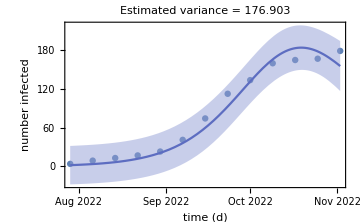

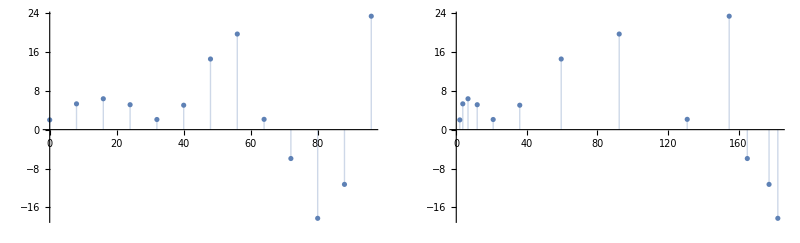

123

```mathematica
fitInfected=NonlinearModelFit[fitInfectedData,{infectedSol[t],5<ζ<21 && 0<λ<21 } ,{{β, 0.8}, {ζ,5},{λ,9}},t];
fitInfected["ParameterTable"]
fitInfected["RSquared"]
fitInfected["AdjustedRSquared"]
(*fitInfected["EstimatedVariance"]*)
fitInfected["BestFitParameters"]
(*fitInfected["BestFit"]*)
fitWithDataPlot[fitInfected,{firstDateInfected,lastDateInfected} ]
residualsPlot[fitInfected]
modelSensitivityPlot[ infectedSol,fitInfected,{{0,100},{-15,190}},{0.1,1,1}]
```

#### Otimização por data, só β

```mathematica
lsActualEquations3 = Join[modelSEIQR2["Equations"]//.KeyDrop[modelSEIQR2["RateRules"],{β}],modelSEIQR2["InitialConditions"]];
ResourceFunction["GridTableForm"][List /@ lsActualEquations3]
asol3 = ParametricNDSolve[lsActualEquations3,{SP,EP,IP,QP, RP},{t,0,120},{β}];
```

# | 1
1 | SP'[t]==0.2 QP[t]-0.000435069 β IP[t] SP[t]
2 | EP'[t]==-(2 EP[t])/13+0.000435069 β IP[t] SP[t]
3 | IP'[t]==EP[t]/13-(4 IP[t])/31
4 | QP'[t]==EP[t]/13-0.329032 QP[t]
5 | RP'[t]==(4 IP[t])/31+(4 QP[t])/31
6 | SP[0]==2286.48
7 | EP[0]==2
8 | IP[0]==2
9 | QP[0]==8
10 | RP[0]==0

```mathematica
totalInfectedOptimized2 = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]],maxInfectiousPeriod] // Normal
(*totalSusceptibleOptimized = SmoothPeriod[Accumulate[TimeSeries[expostosJoined, TemporalRegularity->True]],maxInfectiousPeriod] // Normal*)
firstDateInfected2 = First @ First@Normal[totalInfectedOptimized2]
lastDateInfected2 = First @  Last@ Normal[totalInfectedOptimized2]
fitInfectedData2={toModelTime[firstDateInfected2, #1], #2}& @@@ Normal[totalInfectedOptimized2] //Echo[#, "", Multicolumn]&;
```

{{Thu 11 Aug 2022 00:00:00GMT-3,8},{Thu 1 Sep 2022 00:00:00GMT-3,23},{Thu 22 Sep 2022 00:00:00GMT-3,77},{Thu 13 Oct 2022 00:00:00GMT-3,147},{Thu 3 Nov 2022 00:00:00GMT-3,171}}

Thu 11 Aug 2022 00:00:00GMT-3

Thu 3 Nov 2022 00:00:00GMT-3

{0,8} | {42,77} | {84,171}
{21,23} | {63,147} |

{{Thu 11 Aug 2022 00:00:00GMT-3,8},{Thu 1 Sep 2022 00:00:00GMT-3,23},{Thu 22 Sep 2022 00:00:00GMT-3,77},{Thu 13 Oct 2022 00:00:00GMT-3,147},{Thu 3 Nov 2022 00:00:00GMT-3,171}}

NonlinearModelFit::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the norm of the residual. You may need more than MachinePrecision digits of working precision to meet these tolerances.

| Estimate | Standard Error | t-Statistic | P-Value
β | 0.683228 | 0.0212447 | 32.16 | 5.57306×10^-6

0.977262

0.971578

{β→0.683228}

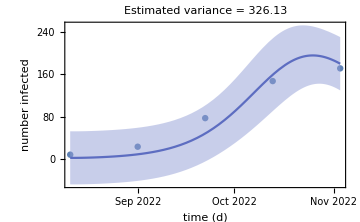

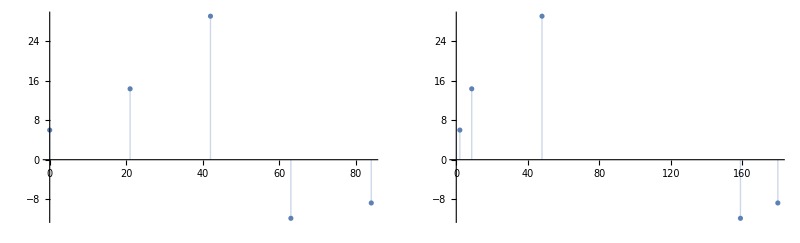

InterpolatingFunction::dmval: Input value {105} lies outside the range of data in the interpolating function. Extrapolation will be used.

360.126

```mathematica
solution := ParametricNDSolve[lsActualEquations3,{SP,EP,IP,QP, RP},{t,First@First@fitInfectedData2,First@Last@fitInfectedData2},{β}];
{susceptible,infectedSol2}= {SP[β],IP[β]} /.solution;
current = Take[totalInfectedOptimized2,5]
fitInfected2=NonlinearModelFit[{toModelTime[First@First@Normal[current], #1], #2}& @@@ Normal[current],infectedSol2[t],{{β,1}},t, Method->"QuasiNewton"];
fitInfected2["ParameterTable"]
fitInfected2["RSquared"]
fitInfected2["AdjustedRSquared"]
fitInfected2["BestFitParameters"]
fitWithDataPlot[fitInfected2,{First@First@Normal[current],First@Last@Normal[current]} ]
residualsPlot[fitInfected2]
(*modelSensitivityPlot[ infectedSol2,fitInfected2,{{First@First@fitInfectedData2,First@Last@fitInfectedData2},{-15,180}},{0.1}]*)

susceptible=SP[N[First@Values[fitInfected2["BestFitParameters"]]]][105] /.solution
```